```mathematica
(*PARAMETERS*)
```

```mathematica
αS:=1(**)
βS:=100(**)
KS:=100(**)
nS:=2(**)
γrE:=1.0/5.0
S[t_]:=2(*Puede ser tambien funcion*)
kE:=20(**)
γE:=1.0/30.0

αRS:=1(**)
βRSR:=100 (**)(*Cuando esta pegado el represor*)
KR:=100(**)
nR:=2(**)
βRSS:=100(**)(*Cuando esta pegado el activador*)
βRSRS:=100(**)(*Cuando estan pegados ambos*)
γrR:=1.0/5.0
kR:=20(**)
γR:=1.0/30.0

kplus:= 0.001(**)(*El k+ del EF*)
kminus:= 0.0005 (**)
KM := 0.001(**) (*KM=k+/(k_+kcat)*)
kcat:=0.01 (**)
KMm :=  0.001(**) (*m es moño, de la reaccion de ZA*)
γB:=1.0/30.0
A[t_]:=10 (**)(*Puede ser funcion*)
```

```mathematica
eqnrE={rE'[t]==αS+βS/(1+(KS/S[t])^nS)-γrE*rE[t]}
eqnpE={pE'[t]==kE*rE[t]-γE*pE[t]}
eqnrR={rR'[t]==αRS+βRSR/((KR/pR[t-100])^nR+1+(S[t]/KS)^nS*(KR/pR[t-100])^nR+(S[t]/KS)^nS)+βRSS/((KS/S[t])^nS+(pR[t-100]/KR)^nR*(KS/S[t])^nS+1+(pR[t-100]/KR)^nR)+βRSRS/((KR/pR[t-100])^nR*(KS/S[t])^nS+(KS/S[t])^nS+(KR/pR[t-100])^nR+1)-γrR*rR[t]}
eqnpR={pR'[t]==kR*rR[t]-γR*pR[t]}
eqnpF={pF'[t]==(-kplus+kminus*KM)*pE[t]*pF[t]+kcat*KMm*pR[t]*A[t]}
eqnpB={pB'[t]==kcat*pE[t]*pF[t]-γB*pB[t]}
initCondrE={rE[0]==0}
initCondpE={pE[0]==0}
initCondrR={rR[0]==0}
initCondpR={pR[0]==0}
initCondpF={pF[0]==0}
initCondpB={pB[0]==0}
```

{rE'[t]==2601/2501-0.2 rE[t]}

{pE'[t]==-0.0333333 pE[t]+20 rE[t]}

{rR'[t]==1+100/(2501/2500+10004/pR[-100+t]^2)+100/(2501+25010000/pR[-100+t]^2)+100/(2501+(2501 pR[-100+t]^2)/10000)-0.2 rR[t]}

{pR'[t]==-0.0333333 pR[t]+20 rR[t]}

{pF'[t]==-0.0009995 pE[t] pF[t]+0.0001 pR[t]}

{pB'[t]==-0.0333333 pB[t]+0.01 pE[t] pF[t]}

{rE[0]==0}

{pE[0]==0}

{rR[0]==0}

{pR[0]==0}

{pF[0]==0}

{pB[0]==0}

```mathematica
tfinal=400
eqns=Join[eqnrE,eqnpE,eqnrR,eqnpR,eqnpF,eqnpB]
initConds = Join[initCondrE,initCondpE,initCondrR,initCondpR,initCondpF,initCondpB]
Solution=NDSolve[Join[eqns,initConds],{rE,pE,rR,pR,pF,pB},{t,0,tfinal}]
```

400

{rE'[t]==2601/2501-0.2 rE[t],pE'[t]==-0.0333333 pE[t]+20 rE[t],rR'[t]==1+100/(2501/2500+10004/pR[-100+t]^2)+100/(2501+25010000/pR[-100+t]^2)+100/(2501+(2501 pR[-100+t]^2)/10000)-0.2 rR[t],pR'[t]==-0.0333333 pR[t]+20 rR[t],pF'[t]==-0.0009995 pE[t] pF[t]+0.0001 pR[t],pB'[t]==-0.0333333 pB[t]+0.01 pE[t] pF[t]}

{rE[0]==0,pE[0]==0,rR[0]==0,pR[0]==0,pF[0]==0,pB[0]==0}

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t ≤ 0..

Power::infy: Infinite expression 1/0^2 encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

{{rE→InterpolatingFunction[{{0., 400.}}, <>],pE→InterpolatingFunction[{{0., 400.}}, <>],rR→InterpolatingFunction[{{0., 400.}}, <>],pR→InterpolatingFunction[{{0., 400.}}, <>],pF→InterpolatingFunction[{{0., 400.}}, <>],pB→InterpolatingFunction[{{0., 400.}}, <>]}}

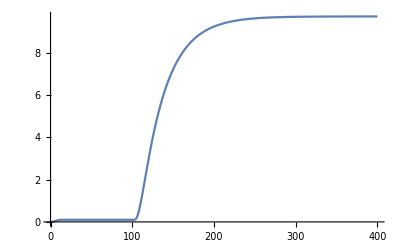

```mathematica
Plot[pF[t]/.Solution,{t,0,tfinal},PlotRange->All]
```